```mathematica
3p^2*(1-p)+ p^3
```

```mathematica
Plot[3 (1-p) p^2+p^3,{p,0,1}]
```

Total influence for majority

2

3

6 (1-p) p

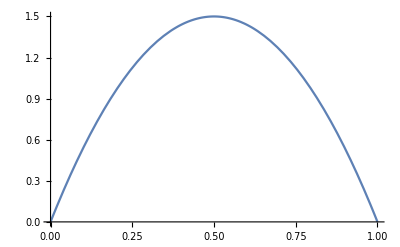

2+2 p-2 p^2

144 (1-p)^3 p^3

```mathematica
k = 2
n = 2k-1
TotInf[p_,n_,k_] = n Binomial[n-1,k-1]p^(k-1)(1-p)^(k-1)
Plot[TotInf[p,n,k],{p,0,1}]

Dmaj3[p_]=2+2p−2p^2
LowerBound[p_,n_,k_] = 4p(1-p)(Sum[Binomial[n-1,k-1]p^(k-1)(1-p)^(k-1),{i,1,n}])^2
Plot[{Dmaj3[p],LowerBound[p,n,k]},{p,0,1},PlotLegends->"Expressions"]
```

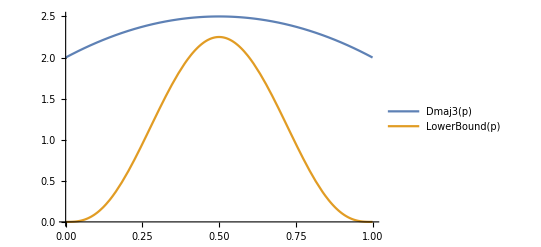

-Graphics-

```mathematica
Export["/home/julia/git/ComplexityOfBooleanFunctions/plots/lowerbound_maj3.png",%16,"PNG"]
```

/home/julia/git/ComplexityOfBooleanFunctions/plots/lowerbound_maj3.png

```mathematica
Export["/home/julia/git/ComplexityOfBooleanFunctions/plots/lowerbound_maj3.png",%390,"PNG"]
```

/home/julia/git/ComplexityOfBooleanFunctions/plots/lowerbound_maj3.png

```mathematica
k = 3
n = 2k-1
LowerBound[p_,n_,k_]=4p(1-p)(Sum[Binomial[n-1,k-1]p^(k-1)(1-p)^(k-1),{i,1,n}])^2
Dmaj5[p_]=3+3p+3p^2−12p^3+6p^4
Plot[{Dmaj5[p],LowerBound[p,n,k]},{p,0,1},PlotLegends->"Expressions"]
```

3

5

3600 (1-p)^5 p^5

3+3 p+3 p^2-12 p^3+6 p^4

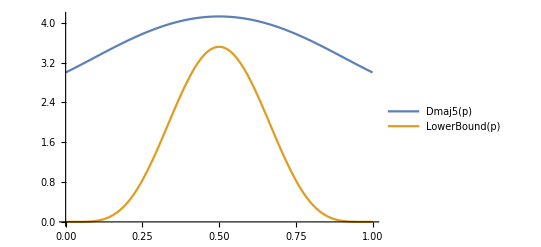

-Graphics-

```mathematica
Export["/home/julia/git/ComplexityOfBooleanFunctions/plots/lowerbound_maj5.png",%18,"PNG"]
```

/home/julia/git/ComplexityOfBooleanFunctions/plots/lowerbound_maj5.png

```mathematica
Export["/home/julia/git/ComplexityOfBooleanFunctions/plots/lowerbound_maj5.png",%396,"PNG"]
```

/home/julia/git/ComplexityOfBooleanFunctions/plots/lowerbound_maj5.png